```mathematica
ClearAll[t,α,γ,Γ,g,s,Ans,initial,v0,p0,u0,num,System2,interpolatingfunctions]
System2[α_,δ_, Α_, g_, s_]:= {u'[t]==s (α-Α) (p[t]-v[t]) (-1+u[t]) u[t],v'[t]==v[t] (-g^2 (-1+p[t]+v[t])+g δ (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])-α (-1+v[t]+(1+p[t]-v[t]) u[t])+Α (p[t] (-1+u[t])+u[t]-v[t] u[t]))),p'[t]==p[t] (-g^2 (-1+p[t]+v[t])+g δ (-1+p[t]+v[t])+s (Α-Α p[t]-α v[t]+s (-1+p[t]+v[t])-(α-Α) (-1+p[t]-v[t]) u[t])), u[0]==u0,v[0]==v0,p[0]==p0}
```

{u'[t]==-0.2 (-1+u[t]) u[t] (p[t]-v[t]),v'[t]==v[t] (0.+0.5 (0.5 (-1+p[t]+v[t])-0.4 (-1+u[t] (1+p[t]-v[t])+v[t])+0.8 (p[t] (-1+u[t])+u[t]-u[t] v[t]))),p'[t]==p[t] (0.+0.5 (0.8-0.8 p[t]+0.4 u[t] (-1+p[t]-v[t])-0.4 v[t]+0.5 (-1+p[t]+v[t]))),u[0]==u0,v[0]==v0,p[0]==p0}

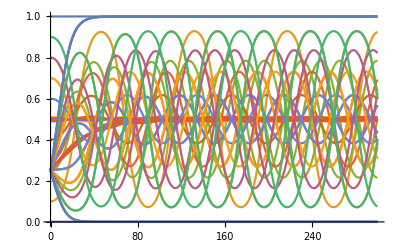

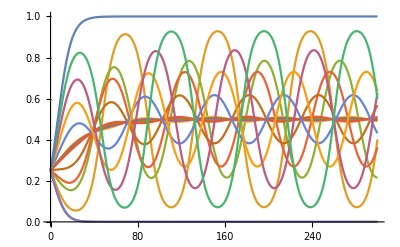

```mathematica
num =System2[0.4, 0.5, 0.8, 0.5, 0.5]
Ans=ParametricNDSolveValue[num,{u[t],v[t],p[t]},{t,0,300},{u0, v0, p0}];
initial = Table[{u0,v0,p0},{u0,{0,0.1,0.25,0.3,0,0.4,0.5,0.51,0.505,0.495,0.49,0.6,0.7,0.8,0.9,1}}, {v0,{0.25}},{p0,{0.25}}]~Flatten~2;
interpolatingfunctions=Ans@@@initial;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column1, specialist 2 is column 3*)
vseries =interpolatingfunctions[[All,2]];
Plot[interpolatingfunctions, {t,0,300}]
Plot[vseries,{t,0,300}]
```